```mathematica
H[k_] = (-μ+2t*Cos[k])PauliMatrix[3]-2Δ*Sin[k]*PauliMatrix[2]
H[k]//MatrixForm
```

{{-μ+2 t Cos[k],2 ⅈ Δ Sin[k]},{-2 ⅈ Δ Sin[k],μ-2 t Cos[k]}}

(-μ+2 t Cos[k] | 2 ⅈ Δ Sin[k]
-2 ⅈ Δ Sin[k] | μ-2 t Cos[k])

```mathematica
ϵ[k_]=√((μ-2 t Cos[k])^2+4 Δ^2 Sin[k]^2){1,-1}
```

{√((μ-2 t Cos[k])^2+4 Δ^2 Sin[k]^2),-√((μ-2 t Cos[k])^2+4 Δ^2 Sin[k]^2)}

```mathematica
MatrixExp[ⅈ π/4*PauliMatrix[2]].H[k].MatrixExp[-ⅈ π/4*PauliMatrix[2]]/√((μ-2 t Cos[k])^2+4 Δ^2 Sin[k]^2)//FullSimplify//MatrixForm
```

(0 | (μ-2 t Cos[k]+2 ⅈ Δ Sin[k])/(√((μ-2 t Cos[k])^2+4 Δ^2 Sin[k]^2))
(μ-2 t Cos[k]-2 ⅈ Δ Sin[k])/(√((μ-2 t Cos[k])^2+4 Δ^2 Sin[k]^2)) | 0)

```mathematica
Clear[δ,Hrs]
(H[k]*Exp[ⅈ*k(x1-x2)]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ k x1-ⅈ k x2)->δ[x1,x2],ⅇ^(-ⅈ k+ⅈ k x1-ⅈ k x2)->δ[x1,x2+1],ⅇ^(ⅈ k+ⅈ k x1-ⅈ k x2)-> δ[x1+1,x2]}
(* assign local real space Hamiltonian *)
Hrs[x1_,x2_]=%;
δ[x_,y_]=If[x==y,1,0];
```

{{-μ δ[x1,x2]+t δ[x1,1+x2]+t δ[1+x1,x2],-Δ δ[x1,1+x2]+Δ δ[1+x1,x2]},{Δ δ[x1,1+x2]-Δ δ[1+x1,x2],μ δ[x1,x2]-t δ[x1,1+x2]-t δ[1+x1,x2]}}

```mathematica
Clear[Hfull]
L = 24;
pbc=False;
Hfull= ConstantArray[0,{L,2,L,2}];
Do[
If[x1>0&&x1≤L,
Hfull[[x1,;;,x2,;;]]+=Hrs[x1,x2];
];

(* the boundary terms *)
If[x1==L+1&&pbc,
Hfull[[1,;;,x2,;;]]+=Hrs[x1,x2];
];
If[x1==0&&pbc,
Hfull[[L,;;,x2,;;]]+=Hrs[x1,x2];
];
,{x1,x2-2,x2+2},{x2,L}]
Hfull=ArrayReshape[Hfull,{2L,2L}];
X=-Range[1,L]+l0;
ΓX=DiagonalMatrix[Flatten[{X,- X}ᵀ]];
TX=DiagonalMatrix[Flatten[{X,X}ᵀ]];
```

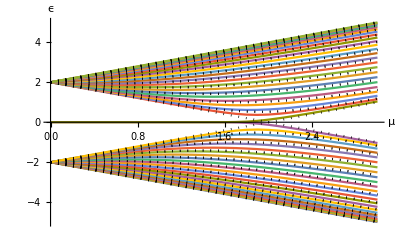

```mathematica
specOBC=Table[Sort[Eigenvalues[N[((Hfull/.{μ->m,Δ->t})/.{t->-1})]]],{m,0,3,0.1}];
specPBC =Table[Sort[Flatten[Table[((ϵ[N[k]]/.{μ->m,Δ->t})/.{t->-1}),{k,0,2π,2π/L}]]],{m,0,3,0.1}];
Show[ListPlot[specOBCᵀ,Joined->True,DataRange->{0,3}],ListPlot[specPBCᵀ,PlotStyle->Directive[Dotted,Black],Joined->True,DataRange->{0,3}],AxesLabel->{"μ","ϵ"}]
```

```mathematica
(*Initial state*)
Clear[ψ0,ψ1]
ψ0=ConstantArray[0,{2L}];
ψ1=ConstantArray[0,{2L}];
l0 = Floor[L/2]; 
ψ0[[2l0-1]]=1;
ψ0[[2l0]]=ⅈ;
ψ0 = Normalize[ψ0];
ψ1[[2l0-1]]=1;
ψ1[[2l0]]=-ⅈ;
ψ1 = Normalize[ψ1];
```

```mathematica
Clear[ψ0ttriv,ψ1ttriv]
ψ0ttriv[t_]=MatrixExp[ⅈ*N[((Hfull/.{μ->5,Δ->t})/.{t->-1})]*t].N[ψ0];
ψ1ttriv[t_]=MatrixExp[ⅈ*N[((Hfull/.{μ->5,Δ->t})/.{t->-1})]*t].N[ψ1];
ψ0tstriv = Table[ψ0t[τ],{τ,0,10,.1}];
ψ1tstriv = Table[ψ1t[τ],{τ,0,10,.1}];
Clear[ψ0t,ψ1t]
ψ0t[t_]=MatrixExp[ⅈ*N[((Hfull/.{μ->1,Δ->t})/.{t->-1})]*t].N[ψ0];
ψ1t[t_]=MatrixExp[ⅈ*N[((Hfull/.{μ->1,Δ->t})/.{t->-1})]*t].N[ψ1];
ψ0ts = Table[ψ0t[τ],{τ,0,10,.1}];
ψ1ts = Table[ψ1t[τ],{τ,0,10,.1}];
```

```mathematica
(* Time evo in the trivial phase... *)
Manipulate[GraphicsRow[{ListPlot[{Abs[ψ0tstriv[[t]]],Abs[ψ1tstriv[[t]]]},PlotRange->Full,PlotLegends->{"|ψ_0|","|ψ_1|"},Joined->True],ListPlot[data={Table[Total[ψ0tstriv[[τ]]*.TX.ψ0tstriv[[τ]]],{τ,1,t}],Table[Total[ψ1tstriv[[τ]]*.TX.ψ1tstriv[[τ]]],{τ,1,t}],Table[Total[ψ0tstriv[[τ]]*.ΓX.ψ0tstriv[[τ]]],{τ,1,t}],Table[Total[ψ1tstriv[[τ]]*.ΓX.ψ1tstriv[[τ]]],{τ,1,t}]},PlotRange->Full,PlotLegends->{"<X>_ψ_0","<X>_ψ_1","<ΓX>_ψ_0","<ΓX>_ψ_1"},AxesLabel->{"t/Δt"},Joined->True]}],{{t,Floor[Length[ψ0ts]/2]},2,Length[ψ0ts],1}]
```

```mathematica
(* Time evo in the topological phase... the same... cazzo *)
Manipulate[GraphicsRow[{ListPlot[{Abs[ψ0ts[[t]]],Abs[ψ1ts[[t]]]},PlotRange->Full,PlotLegends->{"|ψ_0|","|ψ_1|"},Joined->True],ListPlot[data={Table[Total[ψ0ts[[τ]]*.TX.ψ0ts[[τ]]],{τ,1,t}],Table[Total[ψ1ts[[τ]]*.TX.ψ1ts[[τ]]],{τ,1,t}],Table[Total[ψ0ts[[τ]]*.ΓX.ψ0ts[[τ]]],{τ,1,t}],Table[Total[ψ1ts[[τ]]*.ΓX.ψ1ts[[τ]]],{τ,1,t}]},PlotRange->Full,PlotLegends->{"<X>_ψ_0","<X>_ψ_1","<ΓX>_ψ_0","<ΓX>_ψ_1"},AxesLabel->{"t/Δt"},Joined->True]}],{{t,Floor[Length[ψ0ts]/2]},2,Length[ψ0ts],1}]
```